```mathematica
description="Anel El -> Anmu Mu, EW, total cross section, tree";
If[$FrontEnd===Null,$FeynCalcStartupMessages=False;
Print[description];];
If[$Notebooks===False,$FeynCalcStartupMessages=False];
$LoadAddOns={"FeynArts"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
```

FeynCalc 10.2.1 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (27 Mar 2025) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

# Espalhamento e^-ν_e

Vamos forçar escrever de forma mais bonitinha os nossos momentos envolvidos

```mathematica
MakeBoxes[knu,TraditionalForm]:="\!\(\*SubscriptBox[\(k\), \(ν\)]\)";
MakeBoxes[knuf,TraditionalForm]:="\!\(\*SubscriptBox[\(k'\), \(ν\)]\)";
MakeBoxes[pi,TraditionalForm]:="\!\(\*SubscriptBox[\(p\), \(e\)]\)";
MakeBoxes[pf,TraditionalForm]:="\!\(\*SubscriptBox[\(p'\), \(e\)]\)";
```

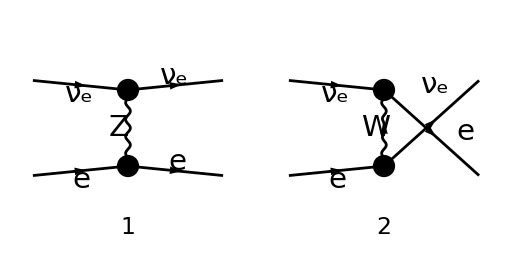

```mathematica
InitializeModel[{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];

diags=InsertFields[CreateTopologies[0,2->2],{F[1,{1}],F[2,{1}]}->{F[1,{1}],F[2,{1}]},InsertionLevel->{Classes},Model->{SM,UnitarySM},GenericModel->{Lorentz,UnitaryLorentz}];
(*DiagramList[diags[[2]]]*)

Paint[diags,ColumnsXRows->{2,1},Numbering->Simple,SheetHeader->None,ImageSize->{512,256}];
```

```mathematica
amp[0]=FCFAConvert[CreateFeynAmp[diags,GaugeRules->{FAGaugeXi[W|Z]->Infinity}],
IncomingMomenta->{knu,pi},
OutgoingMomenta->{knuf,pf},
ChangeDimension->4,
List->False,
SMP->True,
Contract->True,
DropSumOver->True,
FinalSubstitutions->{SMP["e"]->Sqrt[8/Sqrt[2]*SMP["G_F"]*SMP["m_W"]^2 SMP["sin_W"]^2]}]
```

(2 √2 G_F (m_W^2 (φ(OverBar[k'_ν])).(γ̄)^Lor1.(γ̄)^7.(φ(OverBar[p_e],m_e)) (φ(OverBar[p'_e],m_e)).(γ̄)^Lor1.(γ̄)^7.(φ(OverBar[k_ν]))+(φ(OverBar[k'_ν])).(γ̄·(OverBar[k'_ν]-OverBar[p_e])).(γ̄)^7.(φ(OverBar[p_e],m_e)) (φ(OverBar[p'_e],m_e)).(-(γ̄·(OverBar[k'_ν]-OverBar[p_e]))).(γ̄)^7.(φ(OverBar[k_ν]))))/((OverBar[k'_ν]-OverBar[p_e])^2-m_W^2)+1/(m_Z^2 (cos(θ_W)) (sin(θ_W)) ((OverBar[p'_e]-OverBar[p_e])^2-m_Z^2))ⅈ 2^(1/4) √(G_F m_W^2 (sin(θ_W))^2) (m_Z^2 (φ(OverBar[k'_ν])).(γ̄)^Lor1.(γ̄)^7.(φ(OverBar[k_ν])) (φ(OverBar[p'_e],m_e)).((2 ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/(cos(θ_W))-(2 ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^7 (1/2-(sin(θ_W))^2) √(G_F m_W^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_e],m_e))+(φ(OverBar[k'_ν])).(-(γ̄·(OverBar[p'_e]-OverBar[p_e]))).(γ̄)^7.(φ(OverBar[k_ν])) (φ(OverBar[p'_e],m_e)).((2 ⅈ 2^(1/4) (sin(θ_W)) (γ̄·(OverBar[p'_e]-OverBar[p_e])).(γ̄)^6 √(G_F m_W^2 (sin(θ_W))^2))/(cos(θ_W))-(2 ⅈ 2^(1/4) (1/2-(sin(θ_W))^2) (γ̄·(OverBar[p'_e]-OverBar[p_e])).(γ̄)^7 √(G_F m_W^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_e],m_e)))

## Colocando as variáveis de Mandelstan e obtendo a amplitude quadrática

```mathematica
amp[1]=amp[0]//FCE//ReplaceAll[#,{pf-knuf->0}]&//FeynAmpDenominatorExplicit//Series[#,{SMP["m_W"],Infinity,0}]&//Normal
FCClearScalarProducts[];
SetMandelstam[s,t,u,knu,pi,knuf,pf,0,SMP["m_e"],0,SMP["m_e"]]

ampSquared[1] = (amp[1](ComplexConjugate[amp[1]]))// FermionSpinSum[#,ExtraFactor->1/2] & //DiracSimplify // Factor
```

-2 √2 G_F (φ(OverBar[k'_ν])).(γ̄)^Lor1.(γ̄)^7.(φ(OverBar[p_e],m_e)) (φ(OverBar[p'_e],m_e)).(γ̄)^Lor1.(γ̄)^7.(φ(OverBar[k_ν]))-1/(m_Z^2 (cos(θ_W)) (sin(θ_W)) (-4 m_e^2+m_Z^2+t))ⅈ 2^(1/4) √(G_F m_W^2 (sin(θ_W))^2) (m_Z^2 (φ(OverBar[k'_ν])).(γ̄)^Lor1.(γ̄)^7.(φ(OverBar[k_ν])) (φ(OverBar[p'_e],m_e)).((2 ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^6 (sin(θ_W)) √(G_F m_W^2 (sin(θ_W))^2))/(cos(θ_W))-(2 ⅈ 2^(1/4) (γ̄)^Lor1.(γ̄)^7 (1/2-(sin(θ_W))^2) √(G_F m_W^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_e],m_e))+(φ(OverBar[k'_ν])).(-(γ̄·(OverBar[p'_e]-OverBar[p_e]))).(γ̄)^7.(φ(OverBar[k_ν])) (φ(OverBar[p'_e],m_e)).((2 ⅈ 2^(1/4) (sin(θ_W)) (γ̄·(OverBar[p'_e]-OverBar[p_e])).(γ̄)^6 √(G_F m_W^2 (sin(θ_W))^2))/(cos(θ_W))-(2 ⅈ 2^(1/4) (1/2-(sin(θ_W))^2) (γ̄·(OverBar[p'_e]-OverBar[p_e])).(γ̄)^7 √(G_F m_W^2 (sin(θ_W))^2))/((cos(θ_W)) (sin(θ_W)))).(φ(OverBar[p_e],m_e)))

{0,t/2,u/2-m_e^2/2,s/2-m_e^2/2,0,s/2-m_e^2/2,u/2-m_e^2/2,m_e^2,t/2-m_e^2,m_e^2,0,t/2,u/2-m_e^2/2,s/2-m_e^2/2,0,s/2-m_e^2/2,u/2-m_e^2/2,m_e^2,t/2-m_e^2,m_e^2}

1/((cos(θ_W))^4 m_Z^4 (4 m_e^2-m_Z^2-t)^2)2 G_F^2 (128 (cos(θ_W))^4 m_Z^4 m_e^8-64 (cos(θ_W))^4 m_Z^6 m_e^6+16 t m_W^4 m_e^6-256 s (cos(θ_W))^4 m_Z^4 m_e^6-64 t (cos(θ_W))^4 m_Z^4 m_e^6+32 (cos(θ_W))^2 m_W^2 m_Z^4 m_e^6-64 t (cos(θ_W))^2 m_W^2 m_Z^2 m_e^6-64 (cos(θ_W))^2 m_W^2 m_Z^4 (sin(θ_W))^2 m_e^6+8 (cos(θ_W))^4 m_Z^8 m_e^4+128 s (cos(θ_W))^4 m_Z^6 m_e^4+16 t (cos(θ_W))^4 m_Z^6 m_e^4-8 (cos(θ_W))^2 m_W^2 m_Z^6 m_e^4+4 s^2 m_W^4 m_e^4-8 t^2 m_W^4 m_e^4+4 u^2 m_W^4 m_e^4-8 s u m_W^4 m_e^4+128 s^2 (cos(θ_W))^4 m_Z^4 m_e^4+8 t^2 (cos(θ_W))^4 m_Z^4 m_e^4+128 s t (cos(θ_W))^4 m_Z^4 m_e^4+2 m_W^4 m_Z^4 m_e^4-64 s (cos(θ_W))^2 m_W^2 m_Z^4 m_e^4+8 t (cos(θ_W))^2 m_W^2 m_Z^4 m_e^4+16 m_W^4 m_Z^4 (sin(θ_W))^4 m_e^4-8 t m_W^4 m_Z^2 m_e^4-16 s^2 (cos(θ_W))^2 m_W^2 m_Z^2 m_e^4+32 t^2 (cos(θ_W))^2 m_W^2 m_Z^2 m_e^4-16 u^2 (cos(θ_W))^2 m_W^2 m_Z^2 m_e^4+32 s u (cos(θ_W))^2 m_W^2 m_Z^2 m_e^4+16 (cos(θ_W))^2 m_W^2 m_Z^6 (sin(θ_W))^2 m_e^4-8 m_W^4 m_Z^4 (sin(θ_W))^2 m_e^4+128 s (cos(θ_W))^2 m_W^2 m_Z^4 (sin(θ_W))^2 m_e^4+80 t (cos(θ_W))^2 m_W^2 m_Z^4 (sin(θ_W))^2 m_e^4-16 s (cos(θ_W))^4 m_Z^8 m_e^2-64 s^2 (cos(θ_W))^4 m_Z^6 m_e^2-32 s t (cos(θ_W))^4 m_Z^6 m_e^2+16 s (cos(θ_W))^2 m_W^2 m_Z^6 m_e^2+t^3 m_W^4 m_e^2-t u^2 m_W^4 m_e^2-s^2 t m_W^4 m_e^2+2 s t u m_W^4 m_e^2-16 s t^2 (cos(θ_W))^4 m_Z^4 m_e^2-64 s^2 t (cos(θ_W))^4 m_Z^4 m_e^2-4 s m_W^4 m_Z^4 m_e^2+36 s^2 (cos(θ_W))^2 m_W^2 m_Z^4 m_e^2-4 t^2 (cos(θ_W))^2 m_W^2 m_Z^4 m_e^2+4 u^2 (cos(θ_W))^2 m_W^2 m_Z^4 m_e^2+16 s t (cos(θ_W))^2 m_W^2 m_Z^4 m_e^2-8 s u (cos(θ_W))^2 m_W^2 m_Z^4 m_e^2-16 s m_W^4 m_Z^4 (sin(θ_W))^4 m_e^2-16 t m_W^4 m_Z^4 (sin(θ_W))^4 m_e^2-16 u m_W^4 m_Z^4 (sin(θ_W))^4 m_e^2-2 s^2 m_W^4 m_Z^2 m_e^2+2 t^2 m_W^4 m_Z^2 m_e^2-2 u^2 m_W^4 m_Z^2 m_e^2+4 s u m_W^4 m_Z^2 m_e^2-4 t^3 (cos(θ_W))^2 m_W^2 m_Z^2 m_e^2+4 t u^2 (cos(θ_W))^2 m_W^2 m_Z^2 m_e^2+4 s^2 t (cos(θ_W))^2 m_W^2 m_Z^2 m_e^2-8 s t u (cos(θ_W))^2 m_W^2 m_Z^2 m_e^2-32 s (cos(θ_W))^2 m_W^2 m_Z^6 (sin(θ_W))^2 m_e^2-16 t (cos(θ_W))^2 m_W^2 m_Z^6 (sin(θ_W))^2 m_e^2+16 s m_W^4 m_Z^4 (sin(θ_W))^2 m_e^2+8 t m_W^4 m_Z^4 (sin(θ_W))^2 m_e^2-64 s^2 (cos(θ_W))^2 m_W^2 m_Z^4 (sin(θ_W))^2 m_e^2-16 t^2 (cos(θ_W))^2 m_W^2 m_Z^4 (sin(θ_W))^2 m_e^2-32 s t (cos(θ_W))^2 m_W^2 m_Z^4 (sin(θ_W))^2 m_e^2+8 s^2 (cos(θ_W))^4 m_Z^8+16 s^2 t (cos(θ_W))^4 m_Z^6-8 s^2 (cos(θ_W))^2 m_W^2 m_Z^6+8 s^2 t^2 (cos(θ_W))^4 m_Z^4+2 s^2 m_W^4 m_Z^4-8 s^2 t (cos(θ_W))^2 m_W^2 m_Z^4+8 s^2 m_W^4 m_Z^4 (sin(θ_W))^4+8 u^2 m_W^4 m_Z^4 (sin(θ_W))^4+16 s^2 (cos(θ_W))^2 m_W^2 m_Z^6 (sin(θ_W))^2-8 s^2 m_W^4 m_Z^4 (sin(θ_W))^2+16 s^2 t (cos(θ_W))^2 m_W^2 m_Z^4 (sin(θ_W))^2)

## Agora vou plotar coisas

0.00001166

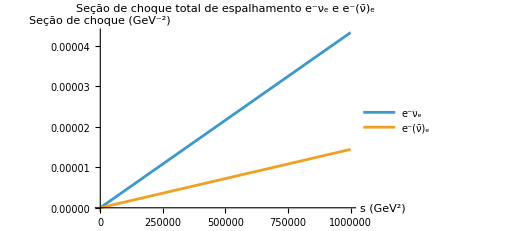

```mathematica
Gf = 1.166*10^(-5) (*GeV^-2*)

sigmaenu[s_]:= Gf^2 * s /Pi
sigmaebarnu[s_]:= Gf^2 *s/(3*Pi)
Plot[{sigmaenu[x],sigmaebarnu[x]},{x,0,10^6}, PlotRange->Automatic,PlotLabel->"Seção de choque total de espalhamento e^-ν_e e e^-(ν̄)_e", AxesLabel->{"s (GeV^2)","Seção de choque (GeV^-2)"}, PlotLegends->{"e^-ν_e","e^-(ν̄)_e"}]
```